### Categorization

Tutorial

Indivaria

Indivaria`

Indivaria/tutorial/19

### Keywords

Details

# Model 1.9-2.0

Model 1.9 and 2.0 are the models for the dynamics of malaria parasites in a patient during treatment with artesunate. They are the modified version of model 1.0-1.2. In these two models, a fraction of parasites can become dormant for a period of time. The dormant stage for these model is defined as the stage that the parasites stop their maturation and cannot be kille by the drug. The dormancy parasites in the models still can be observed in the blood sample.

## Model 1.9

In model 1.9, only the parasites in the ring stage at about 6 to 26 hours of their life-cycle can be dormant with same probability.

parameter names | descriptions
model | model ID
initn | initial load of parasites
lifecycle | parasite life-cycle (hours)
mu | the mean age of parasites on admission (hours)
sigma | the standard deviation of parasites on admission (hours)
pmr | parasite multiplication rate (per life-cycle)
everyh | duration between each dose of artesunate (hours)
ndrug | number of doses 
concfile | the file name of DHA concentration data
killzone | the ranges of the ages of parasites that sensitive to artesunate
gamma | constants related to the slope of EC curve 
ec50 | 50% efficacy concentration
emin | minimum efficacy
emax | maximum efficacy
1/alpha | model constant
runmax | maximum runtime of the model (hours)
lim | the number of parasite at the detection limit (in log10)
dorfrac | the dormancy fraction
dortime | the dormancy period (hours)
outform | the output form

List of parameters of model 1.9.

Model 1.9 has three output form. See table below.

0 | show the number of parasites at each age (1-life-cycle (hours)) over time.
1 | write log10(total number of parasites) of every time step (hour) to "modgen.csv".
2 | show log10(total number of parasites) of every time step (hour).

Example of model 1.9 output.

```mathematica
lsout=IDVL["mod1_9.in"];
```

******INDIVARIA*****

model: 1.9

outform: 2

********************

model: 1.9

initn: 2.30*10^11

pmr: 10

mu: 10

sigma: 5

lifecycle: 48

killzone: {{6,26},{27,38},{39,44}}

concfile: P002.csv

everyh: 24

ndrug: 7

gamma: {5.5,5.5,5.5}

ec50: {20.0,20.0,20.0}

emin: {0.0,0.0,0.0}

emax: {99.99,99.99,99.99}

1/alpha: 5.5

runmax: 100

dorfrac: 0.02

dortime: 120

outform: 2

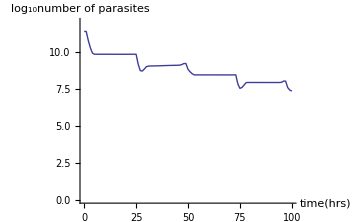

```mathematica
ListPlot[lsout,Joined->True,AxesLabel->{"time(hrs)","log_10number of parasites"},PlotRange->{0,12}]
```

## Model 2.0

In model 2.0, the age distribution of dormancy parasites follows a normal distribution.

parameter names | descriptions
model | model ID
initn | initial load of parasites
lifecycle | parasite life-cycle (hours)
mu | the mean age of parasites on admission (hours)
sigma | the standard deviation of parasites on admission (hours)
pmr | parasite multiplication rate (per life-cycle)
everyh | duration between each dose of artesunate (hours)
ndrug | number of doses 
concfile | the file name of DHA concentration data
killzone | the ranges of the ages of parasites that sensitive to artesunate
gamma | constants related to the slope of EC curve 
ec50 | 50% efficacy concentration
emin | minimum efficacy
emax | maximum efficacy
1/alpha | model constant
runmax | maximum runtime of the model (hours)
lim | the number of parasite at the detection limit (in log10)
dorfrac | the dormancy fraction
dortime | the dormancy period (hours)
dormu | the mean age of dormancy parasites (hours)
dorsig | the standard deviation of the age of dormancy parasites (hours)
outform | the output form

List of parameters of model 2.0.

Model 2.0 has three output form. See table below.

0 | show the number of parasites at each age (1-life-cycle (hours)) over time.
1 | write log10(total number of parasites) of every time step (hour) to "modgen.csv".
2 | show log10(total number of parasites) of every time step (hour).

Example of model 2.0 output.

******INDIVARIA*****

model: 2.

outform: 2

********************

model: 2.

initn: 2.30*10^11

pmr: 10

mu: 10

sigma: 5

lifecycle: 48

killzone: {{6,26},{27,38},{39,44}}

concfile: P002.csv

everyh: 24

ndrug: 7

gamma: {5.5,5.5,5.5}

ec50: {20.0,20.0,20.0}

emin: {0.0,0.0,0.0}

emax: {99.99,99.99,99.99}

1/alpha: 5.5

runmax: 100

dorfrac: 0.02

dortime: 120

dormu: 10

dorsig: 5

outform: 2

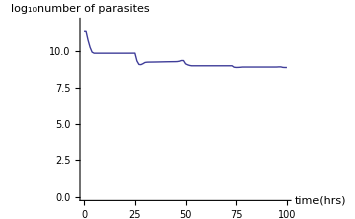

```mathematica
lsout=IDVL["mod2_0.in"];
ListPlot[lsout,Joined->True,AxesLabel->{"time(hrs)","log_10number of parasites"},PlotRange->{0,12}]
```

More About

List of models

Related Tutorials

Using Indivaria

Related Wolfram Education Group Courses